# Data Science and Machine Learning

## Lab session 01: Introduction to Wolfram Language

## Notebook

### What is a notebook?

Wolfram notebooks are interactive documents that support live computation, dynamic interfaces, a variety of input - e.g., raw code, text, image -, and many many functions and options.

### The Notebook interface: Cells

Cells take some input, and once evaluated with Shift+Enter, can provide some output

## Let's get started

### Free-form input

integral of cos(2x)

1/2 Sin[2 x]

```mathematica
Simplify[1/2 Sin[2 x]]
```

Cos[x] Sin[x]

plot of 1/2 sin(2x)

-Graphics-

```mathematica
Show[%3,Background->LightGray]
```

-Graphics-

### Wolfram Language

```mathematica
3*9/8 (* You can write any comment here *)
```

27/8

Tips: By default, WL will give an exact representation of the result. If you want a numerical approximation of your result, use the command: N

```mathematica
N[3*9/8]
```

3.375

```mathematica
Integrate[Cos[2*x],x]
```

1/2 Sin[2 x]

```mathematica
Integrate[Sin[x],{x,0,2 Pi}]
```

0

```mathematica
N[Pi,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
Plot[Sin[x],{x,0,2 Pi}]
```

-Graphics-

```mathematica
Integrate[Sin[x] Cos[x]^2, {x,a,b}]
```

1/3 (Cos[a]^3-Cos[b]^3)

```mathematica
D[Cos[x],x]
```

-Sin[x]

Tips: One cell can contain multiple inputs and generate multiple output cells:

```mathematica
Sin[Pi]
2^3
Range[10]
Plot3D[Sin[x+y],{x,0,2 Pi},{y, 0, 2 Pi}]
```

0

8

{1,2,3,4,5,6,7,8,9,10}

-Graphics3D-

Tips: If you do not want to display a result, use ";" :

```mathematica
Range[3,7]
Range[4,9];
```

{3,4,5,6,7}

image of Alexander von Humboldt

-Graphics-

```mathematica
Binarize[-Graphics-]
```

-Graphics-

```mathematica
WikipediaData["Alexander von Humboldt"]
```

Friedrich Wilhelm Heinrich Alexander von Humboldt (14 September 1769 – 6 May 1859) was a German polymath, geographer, naturalist, explorer, and proponent of Romantic philosophy and science. He was the younger brother of the Prussian minister, philosopher, and linguist Wilhelm von Humboldt (1767–1835). Humboldt's quantitative work on botanical geography laid the foundation for the field of biogeography. Humboldt's advocacy of long-term systematic geophysical measurement laid the foundation for modern geomagnetic and meteorological monitoring.Between 1799 and 1804, Humboldt travelled extensively in the Americas, exploring and describing them for the first time from a modern Western scientific point of view. His description of the journey was written up and published in several volumes over 21 years. Humboldt was one of the first people to propose that the lands bordering the Atlantic Ocean were once joined (South America and Africa in particular).
Humboldt resurrected the use of the word cosmos from the ancient Greek and assigned it to his multivolume treatise, Kosmos, in which he sought to unify diverse branches of scientific knowledge and culture. This important work also motivated a holistic perception of the universe as one interacting entity. He was the first person to describe the phenomenon and cause of human-induced climate change, in 1800 and again in 1831, based on observations generated during his travels.


== Early life and education ==

Alexander von Humboldt was born in Berlin in Prussia on 14 September 1769. He was baptized as a baby in the Lutheran faith, with the Duke of Brunswick serving as godfather.Humboldt's father, Alexander Georg von Humboldt, belonged to a prominent Pomeranian family. Although not one of the titled gentry, he was a major in the Prussian Army, who had served with the Duke of Brunswick. At age 42, Alexander Georg was rewarded for his services in the Seven Years' War with the post of royal chamberlain. He profited from the contract to lease state lotteries and tobacco sales. He first married the daughter of Prussian General Adjutant Schweder. In 1766, Alexander Georg married Maria Elisabeth Colomb, a well-educated woman and widow of Baron Hollwede, with whom she had a son. Alexander Georg and Maria Elisabeth had three children: a daughter, who died young, and then two sons, Wilhelm and Alexander. Her first-born son, Wilhelm and Alexander's half-brother, was something of a ne'er do well, not often mentioned in the family history.Alexander Georg died in 1779, leaving the brothers Humboldt in the care of their emotionally distant mother. She had high ambitions for Alexander and his older brother Wilhelm, hiring excellent tutors, who were Enlightenment thinkers, including Kantian physician Marcus Herz and botanist Carl Ludwig Willdenow, who became one of the most important botanists in Germany. Humboldt's mother expected them to become civil servants of the Prussian state. The money Baron Holwede left to Alexander's mother became, after her death, instrumental in funding Alexander's explorations, contributing more than 70% of his private income.

Due to his youthful penchant for collecting and labeling plants, shells, and insects, Alexander received the playful title of "the little apothecary". Marked for a political career, Alexander studied finance for six months in 1787 at the University of Frankfurt (Oder), which his mother might have chosen less for its academic excellence than its closeness to their home in Berlin. On 25 April 1789, he matriculated at the University of Göttingen, then known for the lectures of C. G. Heyne and anatomist J. F. Blumenbach. His brother Wilhelm was already a student at Göttingen, but they did not interact much, since their intellectual interests were quite different. His vast and varied interests were by this time fully developed.At the University of Göttingen, Humboldt met a Steven Jan van Geuns, a Dutch student of medicine, with whom he travelled to the Rhine in the fall of 1789 and met in Mainz Georg Forster, a naturalist who had been with Captain James Cook on his second voyage. Humboldt's scientific excursion  resulted in his 1790 treatise Mineralogische Beobachtungen über einige Basalte am Rhein (Brunswick, 1790) (Mineralogic Observations on Several Basalts on the River Rhine). The following year, 1790, Humboldt traveled again to Mainz to embark with Forster on a journey to England, Humboldt's first sea voyage, the Netherlands, and France. In England, he met Sir Joseph Banks, president of the Royal Society, who had traveled with Captain Cook; Banks showed Humboldt his huge herbarium, with specimens of the South Sea tropics. The scientific friendship between Banks and Humboldt lasted until Banks's death in 1820, and the two shared botanical specimens for study. Banks also mobilized his scientific contacts in later years to aid Humboldt's work.Humboldt's passion for travel was of long standing. Humboldt's talents were devoted to the purpose of preparing himself as a scientific explorer. With this emphasis, he studied commerce and foreign languages at Hamburg, geology at Freiberg School of Mines in 1791 under A.G. Werner, leader of the Neptunist school of geology; from anatomy at Jena under J.C. Loder; and astronomy and the use of scientific instruments under F.X. von Zach and J.G. Köhler. At Freiberg, he met a number of men who were to prove important to him in his later career, including Spaniard Manuel del Rio, who became director of the School of Mines the crown established in Mexico; Christian Leopold von Buch, who became a regional geologist; and, most importantly, Carl Freiesleben, who became Humboldt's tutor and close friend. During this period, his brother Wilhelm married, but Alexander did not attend the nuptials.


== Travels and work in Europe ==
Humboldt graduated from the Freiberg School of Mines in 1792 and was appointed to a Prussian government position in the Department of Mines as an inspector in Bayreuth and the Fichtel mountains. Humboldt was excellent at his job, with production of gold ore in his first year outstripping the previous eight years. During his period as a mine inspector, Humboldt demonstrated his deep concern for the men laboring in the mines. He opened a free school for miners, paid for out of his own pocket, which became an unchartered government training school for labor. He also sought to establish an emergency relief fund for miners, aiding them following accidents.Humboldt's researches into the vegetation of the mines of Freiberg led to the publication in Latin (1793) of his Florae Fribergensis, accedunt Aphorismi ex Doctrina, Physiologiae Chemicae Plantarum, which was a compendium of his botanical researches. That publication brought him to the attention of Johann Wolfgang von Goethe, who had met Humboldt at the family home when Alexander was a boy, but Goethe was now interested in meeting the young scientist to discuss metamorphism of plants. An introduction was arranged by Humboldt's brother, who lived in the university town of Jena, not far from Goethe. Goethe had developed his own extensive theories on comparative anatomy. Working before Darwin, he believed that animals had an internal force, an urform, that gave them a basic shape and then they were further adapted to their environment by an external force. Humboldt urged him to publish his theories. Together, the two discussed and expanded these ideas. Goethe and Humboldt soon became close friends.
Humboldt often returned to Jena in the years that followed. Goethe remarked about Humboldt to friends that he had never met anyone so versatile. Humboldt's drive served as an inspiration for Goethe. In 1797, Humboldt returned to Jena for three months. During this time, Goethe moved from his residence in Weimar to reside in Jena. Together, Humboldt and Goethe attended university lectures on anatomy and conducted their own experiments. One experiment involved hooking up a frog leg to various metals. They found no effect until the moisture of Humboldt's breath triggered a reaction that caused the frog leg to leap off the table. Humboldt described this as one of his favorite experiments because it was as if he were "breathing life into" the leg.During this visit, a thunderstorm killed a farmer and his wife. Humboldt obtained their corpses and analyzed them in the anatomy tower of the university.

In 1794, Humboldt was admitted to the famous group of intellectuals and cultural leaders of Weimar Classicism. Goethe and Schiller were the key figures at the time. Humboldt contributed (7 June 1795) to Schiller's new periodical, Die Horen, a philosophical allegory entitled Die Lebenskraft, oder der rhodische Genius (The Life Force, or the Rhodian Genius). In this short piece, the only literary story Humboldt ever authored, he tried to summarize the often contradictory results of the thousands of Galvanic experiments he had undertaken.In 1792 and 1797, Humboldt was in Vienna; in 1795 he made a geological and botanical tour through Switzerland and Italy. Although this service to the state was regarded by him as only an apprenticeship to the service of science, he fulfilled its duties with such conspicuous ability that not only did he rise rapidly to the highest post in his department, but he was also entrusted with several important diplomatic missions.Neither brother attended the funeral of their mother on 19 November 1796. Humboldt had not hidden his aversion to his mother, with one correspondent writing of him after her death, "her death... must be particularly welcomed by you". After severing his official connections, he awaited an opportunity to fulfill his long-cherished dream of travel.
Humboldt was able to spend more time on writing up his research. He had used his own body for experimentation on muscular irritability, recently discovered by Luigi Galvani and published his results, Versuche über die gereizte Muskel- und Nervenfaser (Berlin, 1797) (Experiments on Stimulated Muscle and Nerve Fibres), enriched in the French translation with notes by Blumenbach.


== Spanish American expedition, 1799–1804 ==


=== Seeking a foreign expedition ===
With the financial resources to fund his scientific travels, he sought a ship on a major expedition. Meantime, he went to Paris, where his brother Wilhelm was now living. Paris was a great center of scientific learning and his brother and sister-in-law Caroline were well connected in those circles. Louis-Antoine de Bougainville urged Humboldt to accompany him on a major expedition, likely to last five years, but the French revolutionary Directoire placed Nicolas Baudin at the head of it rather than the aging scientific traveler. On the postponement of Captain Baudin's proposed voyage of circumnavigation due to continuing warfare in Europe, which Humboldt had been officially invited to accompany, Humboldt was deeply disappointed. He had already selected scientific instruments for his voyage. He did, however, have a stroke of luck with meeting Aimé Bonpland, the botanist and physician for the voyage.
Discouraged, the two left Paris for Marseilles, where they hoped to join Napoleon Bonaparte in Egypt, but North Africans were in revolt against the French invasion in Egypt and French authorities refused permission to travel. Humboldt and Bonpland eventually found their way to Madrid, where their luck changed spectacularly.


=== Spanish royal authorization, 1799 ===

In Madrid, Humboldt sought authorization to travel to Spain's realms in the Americas; he was aided in obtaining it by the German representative of Saxony at the royal Bourbon court. Baron Forell had an interest in mineralogy and science endeavors and was inclined to help Humboldt. At that time, the Bourbon Reforms sought to reform administration of the realms and revitalize their economies. At the same time, the Spanish Enlightenment was in florescence. For Humboldt "the confluent effect of the Bourbon revolution in government and the Spanish Enlightenment had created ideal conditions for his venture".The Bourbon monarchy had already authorized and funded expeditions, with the Botanical Expedition to the Viceroyalty of Peru to Chile and Peru (1777–88), New Granada (1783–1816), New Spain (Mexico) (1787–1803), and the Malaspina Expedition (1789–94). These were lengthy, state-sponsored enterprises to gather information about plants and animals from the Spanish realms, assess economic possibilities, and provide plants and seeds for the Royal Botanical Garden in Madrid (founded 1755). These expeditions took naturalists and artists, who created visual images as well as careful written observations as well as collecting seeds and plants themselves. Crown officials as early as 1779 issued and systematically distributed Instructions concerning the most secure and economic means to transport live plants by land and sea from the most distant countries, with illustrations, including one for the crates to transport seeds and plants.When Humboldt requested authorization from the crown to travel to Spanish America, most importantly, with his own financing, it was given positive response. Spain under the Habsburg monarchy had guarded its realms against foreigner travelers and intruders. The Bourbon monarch was open to Humboldt's proposal. Spanish Foreign Minister Don Mariano Luis de Urquijo received the formal proposal and Humboldt was presented to the monarch in March 1799. Humboldt was granted access to crown officials and written documentation on Spain's empire. With Humboldt's experience working for the absolutist Prussian monarchy as a government mining official, Humboldt had both the academic training and experience of working well within a bureaucratic structure.

Before leaving Madrid in 1799, Humboldt and Bonpland visited the Natural History Museum, which held results of Martín Sessé y Lacasta and José Mariano Mociño's botanical expedition to New Spain. Humboldt and Bonpland met Hipólito Ruiz López and José Antonio Pavón y Jiménez of the royal expedition to Peru and Chile in person in Madrid and examined their botanical collections.


=== Venezuela, 1799–1800 ===

Armed with authorization from the King of Spain, Humboldt and Bonpland made haste to sail, taking the ship Pizarro from A Coruña, on 5 June 1799. The ship stopped six days on the island of Tenerife, where Humboldt climbed the volcano Teide, and then sailed on to the New World, landing at Cumaná, Venezuela, on 16 July.
The ship's destination was not originally Cumaná, but an outbreak of typhoid on board meant that the captain changed course from Havana to land in northern South America. Humboldt had not mapped out a specific plan of exploration, so that the change did not upend a fixed itinerary. He later wrote that the diversion to Venezuela made possible his explorations along the Orinoco River to the border of Portuguese Brazil. With the diversion, the Pizarro encountered two large dugout canoes each carrying 18 Guayaqui Indians. The Pizarro's captain accepted the offer of one of them to serve as pilot. Humboldt hired this Indian, named Carlos del Pino, as a guide.Venezuela from the 16th to the 18th centuries was a relative backwater compared to the seats of the Spanish viceroyalties based in New Spain (Mexico) and Peru, but during the Bourbon reforms, the northern portion of Spanish South America was reorganized administratively, with the 1777 establishment of a captaincy-general based at Caracas. A great deal of information on the new jurisdiction had already been compiled by François de Pons, but was not published until 1806.Rather than describe the administrative center of Caracas, Humboldt started his researches with the valley of Aragua, where export crops of sugar, coffee, cacao, and cotton were cultivated. Cacao plantations were the most profitable, as world demand for chocolate rose. It is here that Humboldt is said to have developed his idea of human-induced climate change. Investigating evidence of a rapid fall in the water level of valley's Lake Valencia, Humboldt credited the desiccation to the clearance of tree cover and to the inability of the exposed soils to retain water. With their clear cutting of trees, the agriculturalists were removing the woodland's "threefold" moderating influence upon temperature: cooling shade, evaporation and radiation.Humboldt visited the mission at Caripe and explored the Guácharo cavern, where he found the oilbird, which he was to make known to science as Steatornis caripensis. Also described the Guanoco asphalt lake as "The spring of the good priest" ("Quelle des guten Priesters"). Returning to Cumaná, Humboldt observed, on the night of 11–12 November, a remarkable meteor shower (the Leonids). He proceeded with Bonpland to Caracas where he climbed the Avila mount with the young poet Andrés Bello, the former tutor of Simón Bolívar, who later became the leader of independence in northern South America. Humboldt met the Venezuelan Bolívar himself in 1804 in Paris and spent time with him in Rome. The documentary record does not support the supposition that Humboldt inspired Bolívar to participate in the struggle for independence, but it does indicate Bolívar's admiration for Humboldt's production of new knowledge on Spanish America.In February 1800, Humboldt and Bonpland left the coast with the purpose of exploring the course of the Orinoco River and its tributaries. This trip, which lasted four months and covered 1,725 miles (2,776 km) of wild and largely uninhabited country, had an aim of establishing the existence of the Casiquiare canal (a communication between the water systems of the rivers Orinoco and Amazon). Although, unbeknownst to Humboldt, this existence had been established decades before, his expedition had the important results of determining the exact position of the bifurcation, and documenting the life of several native tribes such as the Maipures and their extinct rivals the Atures (several words of the latter tribe were transferred to Humboldt by one parrot). Around 19 March 1800, Humboldt and Bonpland discovered dangerous electric eels, whose shock could kill a man. To catch them, locals suggested they drive wild horses into the river, which brought the eels out from the river mud, and resulted in a violent confrontation of eels and horses, some of which died. Humboldt and Bonpland captured and dissected some eels, which retained their ability to shock; both received potentially dangerous electric shocks during their investigations. The encounter made Humboldt think more deeply about electricity and magnetism, typical of his ability to extrapolate from an observation to more general principles. Humboldt returned to the incident in several of his later writings, including his travelogue Personal Narrative (1814–29), Views of Nature (1807), and Aspects of Nature (1849).Two months later, they explored the territory of the Maypures and that of the then-recently extinct Aturès Indians. Humboldt laid to rest the persistent myth of Walter Raleigh's Lake Parime by proposing that the seasonal flooding of the Rupununi savannah had been misidentified as a lake.


=== Cuba, 1800, 1804 ===

On 24 November 1800, the two friends set sail for Cuba, landing on 19 December, where they met fellow botanist and plant collector John Fraser. Fraser and his son had been shipwrecked off the Cuban coast, and did not have a license to be in the Spanish Indies. Humboldt, who was already in Cuba, interceded with crown officials in Havana, as well as giving them money and clothing. Fraser obtained permission to remain in Cuba and explore. Humboldt entrusted Fraser with taking two cases of Humboldt and Bonpland's botanical specimens to England when he returned, for eventual conveyance to the German botanist Willdenow in Berlin. Humboldt and Bonpland stayed in Cuba until 5 March 1801, when they left for the mainland of northern South America again, arriving there on 30 March.
Humboldt is considered to be the "second discoverer of Cuba" due to the scientific and social research he conducted on this Spanish colony. During an initial three-month stay at Havana, his first tasks were to properly survey that city and the nearby towns of Guanabacoa, Regla, and Bejucal. He befriended Cuban landowner and thinker Francisco de Arango y Parreño; together they visited the Guines area in south Havana, the valleys of Matanzas Province, and the Valley of the Sugar Mills in Trinidad. Those three areas were, at the time, the first frontier of sugar production in the island. During those trips, Humboldt collected statistical information on Cuba's population, production, technology and trade, and with Arango, made suggestions for enhancing them. He predicted that the agricultural and commercial potential of Cuba was huge and could be vastly improved with proper leadership in the future.
On their way back to Europe from Mexico on their way to the United States, Humboldt and Bonpland stopped again in Cuba, leaving from the port of Veracruz and arriving in Cuba on 7 January 1804, staying until 29 April 1804. In Cuba, he collected plant material and made extensive notes. During this time, he socialized with his scientific and landowner friends, conducted mineralogical surveys, and finished his vast collection of the island's flora and fauna that he eventually published as Essai politique sur l'îsle de Cuba.


=== The Andes, 1801–1803 ===

After their first stay in Cuba of three months, they returned to the mainland at Cartagena de Indias (now in Colombia), a major center of trade in northern South America. Ascending the swollen stream of the Magdalena River to Honda, they arrived in Bogotá on 6 July 1801, where they met the Spanish botanist José Celestino Mutis, head of the Royal Botanical Expedition to New Granada, staying there until 8 September 1801. Mutis was generous with his time and gave Humboldt access to the huge pictorial record he had compiled since 1783. Mutis was based in Bogotá, but as with other Spanish expeditions, he had access to local knowledge and a workshop of artists, who created highly accurate and detailed images. This type of careful recording meant that even if specimens were not available to study at a distance, "because the images traveled, the botanists did not have to". Humboldt was astounded at Mutis's accomplishment; when Humboldt published his first volume on botany, he dedicated it to Mutis "as a simply mark of our admiration and acknowledgement".Humboldt had hopes of connecting with the French sailing expedition of Baudin, now finally underway, so Bonpland and Humboldt hurried to Ecuador. They crossed the frozen ridges of the Cordillera Real, they reached Quito on 6 January 1802, after a tedious and difficult journey.
Their stay in Ecuador was marked by the ascent of Pichincha and their climb of Chimborazo, where Humboldt and his party reached an altitude of 19,286 feet (5,878 m). This was a world record at the time (for a westerner—Incas had reached much higher altitudes centuries before), but 1000 feet short of the summit. Humboldt's journey concluded with an expedition to the sources of the Amazon en route for Lima, Peru.At Callao, the main port for Peru, Humboldt observed the transit of Mercury on 9 November and studied the fertilizing properties of guano, rich in nitrogen, the subsequent introduction of which into Europe was due mainly to his writings.


=== New Spain (Mexico), 1803–1804 ===

Humboldt and Bonpland had not intended to go to New Spain, but when they were unable to join a voyage to the Pacific, they left the Ecuadorian port of Guayaquil and headed for Acapulco on Mexico's west coast. Even before Humboldt and Bonpland started on their way to New Spain's capital on Mexico's central plateau, Humboldt realized the captain of the vessel that brought them to Acapulco had reckoned its location incorrectly. Since Acapulco was the main west-coast port and the terminus of the Asian trade from the Spanish Philippines, having accurate maps of its location was extremely important. Humboldt set up his instruments, surveying the deep-water bay of Acapulco, to determine its longitude.Humboldt and Bonpland landed in Acapulco on 15 February 1803, and from there they went to Taxco, a silver-mining town in modern Guerrero. In April 1803, he visited Cuernavaca, Morelos. Impressed by its climate, he nicknamed the city the City of Eternal Spring. Humboldt and Bonpland arrived in Mexico City, having been officially welcomed via a letter from the king's representative in New Spain, Viceroy Don José de Iturrigaray. Humboldt was also given a special passport to travel throughout New Spain and letters of introduction to intendants, the highest officials in New Spain's administrative districts (intendancies). This official aid to Humboldt allowed him to have access to crown records, mines, landed estates, canals, and Mexican antiquities from the prehispanic era. Humboldt read the writings of Bishop-elect of the important diocese of Michoacan Manuel Abad y Queipo, a classical liberal, that were directed to the crown for the improvement of New Spain.They spent the year in the viceroyalty, traveling to different Mexican cities in the central plateau and the northern mining region. The first journey was from Acapulco to Mexico City, through what is now the Mexican state of Guerrero. The route was suitable only for mule train, and all along the way, Humboldt took measurements of elevation. When he left Mexico a year later in 1804, from the east coast port of Veracruz, he took a similar set of measures, which resulted in a chart in the Political Essay, the physical plan of Mexico with the dangers of the road from Acapulco to Mexico City, and from Mexico City to Veracruz. This visual depiction of elevation was part of Humboldt's general insistence that the data he collected be presented in a way more easily understood than statistical charts. A great deal of his success in gaining a more general readership for his works was his understanding that "anything that has to do with extent or quantity can be represented geometrically. Statistical projections [charts and graphs], which speak to the senses without tiring the intellect have the advantage of bringing attention to a large number of important facts".Humboldt was impressed with Mexico City, which at the time was the largest city in the Americas, and one that could be counted as modern. He declared "no city of the new continent, without even excepting those of the United States, can display such great and solid scientific establishments as the capital of Mexico". He pointed to the Royal College of Mines, the Royal Botanical Garden and the Royal Academy of San Carlos as exemplars of a metropolitan capital in touch with the latest developments on the continent and insisting on its modernity. He also recognized important creole savants in Mexico, including José Antonio de Alzate y Ramírez, who died in 1799, just before Humboldt's visit; Miguel Velásquez de León; and Antonio de León y Gama.Humboldt spent time at the Valenciana silver mine in Guanajuato, central New Spain, at the time the most important in the Spanish empire. The bicentennial of his visit in Guanajuato was celebrated with a conference at the University of Guanajuato, with Mexican academics highlighting various aspects of his impact on the city. Humboldt could have simply examined the geology of the fabulously rich mine, but he took the opportunity to study the entire mining complex as well as analyze mining statistics of its output. His report on silver mining is a major contribution, and considered the strongest and best informed section of his Political Essay. Although Humboldt was himself a trained geologist and mining inspector, he drew on mining experts in Mexico. One was Fausto Elhuyar, then head of the General Mining Court in Mexico City, who, like Humboldt was trained in Freiberg. Another was Andrés Manuel del Río, director of Royal College of Mines, whom Humboldt knew when they were both students in Freiberg. The Bourbon monarchs had established the mining court and the college to elevate mining as a profession, since revenues from silver constituted the crown's largest source of income. Humboldt also consulted other German mining experts, who were already in Mexico. While Humboldt was a welcome foreign scientist and mining expert, the Spanish crown had established fertile ground for Humboldt's investigations into mining.
Spanish America's ancient civilizations were a source of interest for Humboldt, who included images of Mexican manuscripts (or codices) and Inca ruins in his richly illustrated Vues des cordillères et monuments des peuples indigènes de l'Amerique (1810–1813), the most experimental of Humboldt's publications, since it does not have "a single ordering principle" but his opinions and contentions based on observation. For Humboldt, a key question was the influence of climate on the development of these civilizations. When he published his Vues des cordillères, he included a color image of the Aztec calendar stone, which had been discovered buried in the main plaza of Mexico City in 1790, along with select drawings of the Dresden Codex and others he sought out later in European collections. His aim was to muster evidence that these pictorial and sculptural images could allow the reconstruction of prehispanic history. He sought out Mexican experts in the interpretation of sources from there, especially Antonio Pichardo, who was the literary executor of Antonio de León y Gama's work. For American-born Spaniards (creoles) who were seeking sources of pride in Mexico's ancient past, Humboldt's recognition of these ancient works and dissemination in his publications was a boon. He read the work of exiled Jesuit Francisco Javier Clavijero, which celebrated Mexico's prehispanic civilization, and which Humboldt invoked to counter the pejorative assertions about the new world by Buffon, de Pauw, and Raynal. Humboldt ultimately viewed both the prehispanic realms of Mexico and Peru as despotic and barbaric. However, he also drew attention to indigenous monuments and artifacts as cultural productions that had "both ... historical and artistic significance".One of his most widely read publications resulting from his travels and investigations in Spanish America was the Essai politique sur le royaum de la Nouvelle Espagne, quickly translated to English as Political Essay on the Kingdom of New Spain (1811). This treatise was the result of Humboldt's own investigations as well as the generosity of Spanish colonial officials for statistical data.


=== The United States, 1804 ===

Leaving from Cuba, Humboldt decided to take an unplanned short visit to the United States. Knowing that the current U.S. president, Thomas Jefferson, was himself a scientist, Humboldt wrote to him saying that he would be in the United States. Jefferson warmly replied, inviting him to visit the White House in the nation's new capital. In his letter Humboldt had gained Jefferson's interest by mentioning that he had discovered mammoth teeth near the Equator. Jefferson had previously written that he believed mammoths had never lived so far south. Humboldt had also hinted at his knowledge of New Spain.Arriving in Philadelphia, which was a center of learning in the U.S., Humboldt met with some of the major scientific figures of the era, including chemist and anatomist Caspar Wistar, who pushed for compulsory smallpox vaccination, and botanist Benjamin Smith Barton, as well as physician Benjamin Rush, a signer of the Declaration of Independence, who wished to hear about cinchona bark from a South American tree, which cured fevers. Humboldt's treatise on cinchona was published in English in 1821.After arriving in Washington D.C, Humboldt held numerous intense discussions with Jefferson on both scientific matters and also his year-long stay in New Spain. Jefferson had only recently concluded the Louisiana Purchase, which now placed New Spain on the southwest border of the United States. The Spanish minister in Washington, D.C. had declined to furnish the U.S. government with information about Spanish territories, and access to the territories was strictly controlled. Humboldt was able to supply Jefferson with the latest information on the population, trade agriculture and military of New Spain. This information would later be the basis for his Essay on the Political Kingdom of New Spain (1810). 
Jefferson was unsure of where the border of the newly-purchased Louisiana was precisely, and Humboldt wrote him a two-page report on the matter. Jefferson would later refer to Humboldt as "the most scientific man of the age". Albert Gallatin, Secretary of the Treasury, said of Humboldt "I was delighted and swallowed more information of various kinds in less than two hours than I had for two years past in all I had read or heard." Gallatin, in turn, supplied Humboldt with information he sought on the United States.After six weeks, Humboldt set sail for Europe from the mouth of the Delaware and landed at Bordeaux on 3 August 1804.


=== Travel diaries ===
Humboldt kept a detailed diary of his sojourn to Spanish America, running some 4,000 pages, which he drew on directly for his multiple publications following the expedition. The leather-bound diaries themselves are now in Germany, having been returned from Russia to East Germany, where they were taken by the Red Army after World War II. Following German reunification, the diaries were returned to a descendant of Humboldt. For a time, there was concern about their being sold, but that was averted. A government-funded project to digitize the Spanish American expedition as well as his later Russian expedition has been undertaken (2014–2017) by the University of Potsdam and the German State Library–Prussian Cultural Heritage Foundation.


=== Achievements of the Latin American expedition ===

Humboldt's decades' long endeavor to publish the results of this expedition not only resulted in multiple volumes, but also made his international reputation in scientific circles. Humboldt came to be well-known with the reading public as well, with popular, densely illustrated, condensed versions of his work in multiple languages. Bonpland, his fellow scientist and collaborator on the expedition, collected botanical specimens and preserved them, but unlike Humboldt who had a passion to publish, Bonpland had to be prodded to do the formal descriptions. Many scientific travelers and explorers produced huge visual records, which remained unseen by the general public until the late nineteenth century, in the case of the Malaspina Expedition, and even the late twentieth century, when Mutis's botanical, some 12,000 drawings from New Granada, was published. Humboldt, by contrast, published immediately and continuously, using and ultimately exhausting his personal fortune, to produce both scientific and popular texts. Humboldt's name and fame were made by his travels to Spanish America, particularly his publication of the Political Essay on the Kingdom of New Spain. His image as the premier European scientist was a later development.For the Bourbon crown, which had authorized the expedition, the returns were not only tremendous in terms of sheer volume of data on their New World realms, but in dispelling the vague and pejorative assessments of the New World by Guillaume-Thomas Raynal, Georges-Louis Leclerc, Comte de Buffon, and William Robertson. The achievements of the Bourbon regime, especially in New Spain, were evident in the precise data Humboldt systematized and published.This memorable expedition may be regarded as having laid the foundation of the sciences of physical geography, plant geography, and meteorology. Key to that was Humboldt's meticulous and systematic measurement of phenomena with the most advanced instruments then available. He closely observed plant and animal species in situ, not just in isolation, noting all elements in relation to one other. He collected specimens of plants and animals, dividing the growing collection so that if a portion was lost, other parts might survive.

Humboldt saw the need for an approach to science that could account for the harmony of nature among the diversity of the physical world. For Humboldt, "the unity of nature" meant that it was the interrelation of all physical sciences—such as the conjoining between biology, meteorology and geology—that determined where specific plants grew. He found these relationships by unraveling myriad, painstakingly collected data, data extensive enough that it became an enduring foundation upon which others could base their work. Humboldt viewed nature holistically, and tried to explain natural phenomena without the appeal to religious dogma. He believed in the central importance of observation, and as a consequence had amassed a vast array of the most sophisticated scientific instruments then available. Each had its own velvet lined box and was the most accurate and portable of its time; nothing quantifiable escaped measurement. According to Humboldt, everything should be measured with the finest and most modern instruments and sophisticated techniques available, for that collected data was the basis of all scientific understanding.
This quantitative methodology would become known as Humboldtian science. Humboldt wrote "Nature herself is sublimely eloquent. The stars as they sparkle in firmament fill us with delight and ecstasy, and yet they all move in orbit marked out with mathematical precision."

His Essay on the Geography of Plants (published first in French and then German, both in 1807) was based on the then novel idea of studying the distribution of organic life as affected by varying physical conditions. This was most famously depicted in his published cross-section of Chimborazo, approximately two feet by three feet (54 cm x 84 cm) color pictorial, he called Ein Naturgemälde der Anden and what is also called the Chimborazo Map. It was a fold-out at the back of the publication. Humboldt first sketched the map when he was in South America, which included written descriptions on either side of the cross-section of Chimborazo. These detailed the information on temperature, altitude, humidity, atmosphere pressure, and the animal and plants (with their scientific names) found at each elevation. Plants from the same genus appear at different elevations. The depiction is on an east-west axis going from the Pacific coast lowlands to the Andean range of which Chimborazo was a part, and the eastern Amazonian basin. Humboldt showed the three zones of coast, mountains, and Amazonia, based on his own observations, but he also drew on existing Spanish sources, particularly Pedro Cieza de León, which he explicitly referred to. The Spanish American scientist Francisco José de Caldas had also measured and observed mountain environments and had earlier come to similar ideas about environmental factors in the distribution of life forms. Humboldt was thus not putting forward something entirely new, but it is argued that his finding is not derivative either. The Chimborazo map displayed complex information in an accessible fashion. The map was the basis for comparison with other major peaks. "The Naturgemälde showed for the first time that nature was a global force with corresponding climate zones across continents." Another assessment of the map is that it "marked the beginning of a new era of environmental science, not only of mountain ecology but also of global-scale biogeophysical patterns and processes."

By his delineation (in 1817) of isothermal lines, he at once suggested the idea and devised the means of comparing the climatic conditions of various countries. He first investigated the rate of decrease in mean temperature with the increase in elevation above sea level, and afforded, by his inquiries regarding the origin of tropical storms, the earliest clue to the detection of the more complicated law governing atmospheric disturbances in higher latitudes. This was a major contribution to climatology.His discovery of the decrease in intensity of Earth's magnetic field from the poles to the equator was communicated to the Paris Institute in a memoir read by him on 7 December 1804. Its importance was attested by the speedy emergence of rival claims.His services to geology were based on his attentive study of the volcanoes of the Andes and Mexico, which he observed and sketched, climbed, and measured with a variety of instruments. By climbing Chimborazo, he established an altitude record which became the basis for measurement of other volcanoes in the Andes and the Himalayas. As with other aspects of his investigations, he developed methods to show his synthesized results visually, using the graphic method of geologic-cross sections. He showed that volcanoes fell naturally into linear groups, presumably corresponding with vast subterranean fissures; and by his demonstration of the igneous origin of rocks previously held to be of aqueous formation, he contributed largely to the elimination of erroneous views, such as Neptunism.Humboldt was a significant contributor to cartography, creating maps, particularly of New Spain, that became the template for later mapmakers in Mexico. His careful recording of latitude and longitude led to accurate maps of Mexico, the port of Acapulco, the port of Veracruz, and the Valley of Mexico, and a map showing trade patterns among continents. His maps also included schematic information on geography, converting areas of administrative districts (intendancies) using proportional squares. The U.S. was keen to see his maps and statistics on New Spain, since they had implication for territorial claims following the Louisiana Purchase. Later in life, Humboldt published three volumes (1836–39) examining sources that dealt with the early voyages to the Americas, pursuing his interest in nautical astronomy in the fifteenth and sixteenth centuries. His research yielded the origin of the name "America", put on a map of the Americas by Martin Waldseemüller.

Humboldt conducted a census of the indigenous and European inhabitants in New Spain, publishing a schematized drawing of racial types and populations distribution, grouping them by region and social characteristics. He estimated the population to be six million individuals. He estimated Indians to be forty percent of New Spain's population, but their distribution being uneven; the most dense were in the center and south of Mexico, the least dense in the north. He presented these data in chart form, for easier understanding. He also surveyed the non-Indian population, categorized as Whites (Spaniards), Negroes, and castes (castas). American-born Spaniards, so-called creoles had been painting depictions of mixed-race family groupings in the eighteenth century, showing father of one racial category, mother of another, and the offspring in a third category in hierarchical order, so racial hierarchy was an essential way elites viewed Mexican society. Humboldt reported that American-born Spaniards were legally racial equals of those born in Spain, but the crown policy since the Bourbons took the Spanish throne privileged those born in Iberia. Humboldt observed that "the most miserable European, without education and without intellectual cultivation, thinks himself superior to whites born in the new continent". The truth in this assertion, and the conclusions derived from them, have been often disputed as superficial, or politically motivated, by some authors, considering that between 40% and 60% of high offices in the new world were held by creoles.
The enmity between some creoles and the peninsular-born whites increasingly became an issue in the late period of Spanish rule, with creoles increasingly alienated from the crown. Humboldt's assessment was that royal government abuses and the example of a new model of rule in the United States were eroding the unity of whites in New Spain. Humboldt's writings on race in New Spain were shaped by the memorials of the classical liberal, enlightened Bishop-elect of Michoacán, Manuel Abad y Queipo, who personally presented Humboldt with his printed memorials to the Spanish crown critiquing social and economic conditions and his recommendations for eliminating them.One scholar says that his writings contain fantastical descriptions of America, while leaving out its inhabitants, stating that Humboldt, coming from the Romantic school of thought, believed '... nature is perfect till man deforms it with care'. The further assessment is that he largely neglected the human societies amidst nature. Views of indigenous peoples as 'savage' or 'unimportant' leaves them out of the historical picture. Other scholars counter that Humboldt dedicated large parts of his work to describing the conditions of slaves, indigenous peoples, mixed-race castas, and society in general. He often showed his disgust for the slavery and inhumane conditions in which indigenous peoples and others were treated and he often criticized Spanish colonial policies.Humboldt was not primarily an artist, but he could draw well, allowing him to record a visual record of particular places and their natural environment. Many of his drawings became the basis for illustrations of his many scientific and general publications. Artists whom Humboldt influenced, such as Johann Moritz Rugendas, followed in his path and painted the same places Humboldt had visited and recorded, such as the basalt formations in Mexico, which was an illustration in his Vues des Cordillères.The editing and publication of the encyclopedic mass of scientific, political and archaeological material that had been collected by him during his absence from Europe was now Humboldt's most urgent desire. After a short trip to Italy with Joseph Louis Gay-Lussac for the purpose of investigating the law of magnetic declination and a stay of two and a half years in Berlin, in the spring of 1808, he settled in Paris. His purpose for being located there was to secure the scientific cooperation required for bringing his great work through the press. This colossal task, which he at first hoped would occupy but two years, eventually cost him twenty-one, and even then it remained incomplete.

		
		
		


== Scholarly and public recognition ==

During his lifetime Humboldt became one of the most famous men in Europe. Academies, both native and foreign, were eager to elect him to their membership, the first being The American Philosophical Society in Philadelphia, which he visited at the tail end of his travel through the Americas. He was elected to the Prussian Academy of Sciences in 1805.Over the years other learned societies in the U.S. elected him a member, including the American Antiquarian Society (Worcester, MA) in 1816; the Linnean Society of London in 1818; the New York Historical Society in 1820; a Foreign Honorary Member of the American Academy of Arts and Sciences in 1822.; the American Ethnological Society (New York) in 1843; and the American Geographical and Statistical Society, (New York) in 1856. He was elected a foreign member of the Royal Swedish Academy of Sciences in 1810. The Royal Society, whose president Sir Joseph Banks had aided Humboldt as a young man, now welcomed him as a foreign member.After Mexican independence from Spain in 1821, the Mexican government recognized him with high honors for his services to the nation. In 1827, the first President of Mexico, Guadalupe Victoria granted Humboldt Mexican citizenship and in 1859, the President of Mexico, Benito Juárez, named Humboldt a hero of the nation (benemérito de la nación). The gestures were purely honorary; he never returned to the Americas following his expedition.
Importantly for Humboldt's long-term financial stability, King Frederick William III of Prussia conferred upon him the honor of the post of royal chamberlain, without at the time exacting the duties. The appointment had a pension of 2,500 thalers, afterwards doubled. This official stipend became his main source of income in later years when he exhausted his fortune on the publications of his research. Financial necessity forced his permanent relocation to Berlin in 1827 from Paris. In Paris he found not only scientific sympathy, but the social stimulus which his vigorous and healthy mind eagerly craved. He was equally in his element as the lion of the salons and as the savant of the Institut de France and the observatory.
On 12 May 1827 he settled permanently in Berlin, where his first efforts were directed towards the furtherance of the science of terrestrial magnetism. In 1827, he began giving public lectures in Berlin, which became the basis for his last major publication, Kosmos (1845–62).For many years, it had been one of his favorite schemes to secure, by means of simultaneous observations at distant points, a thorough investigation of the nature and law of "magnetic storms" (a term invented by him to designate abnormal disturbances of Earth's magnetism). The meeting at Berlin, on 18 September 1828, of a newly formed scientific association, of which he was elected president, gave him the opportunity of setting on foot an extensive system of research in combination with his diligent personal observations. His appeal to the Russian government, in 1829, led to the establishment of a line of magnetic and meteorological stations across northern Asia. Meanwhile, his letter to the Duke of Sussex, then (April 1836) president of the Royal Society, secured for the undertaking, the wide basis of the British dominions.
The Encyclopædia Britannica, Eleventh Edition, observes, "Thus that scientific conspiracy of nations which is one of the noblest fruits of modern civilization was by his exertions first successfully organized". However, earlier examples of international scientific cooperation exist, notably the 18th-century observations of the transits of Venus.
In 1869, the 100th year of his birth, Humboldt's fame was so great that cities all over America celebrated his birth with large festivals. In New York City, a bust of his head was unveiled in Central Park.Scholars have speculated about the reasons for Humboldt's declining renown among the public. Sandra Nichols has argued that there are three reasons for this. First, a trend towards specialization in scholarship. Humboldt was a generalist who connected many disciplines in his work. Today, academics have become more and more focused on narrow fields of work. Humboldt combined ecology, geography and even social sciences. Second, a change in writing style. Humboldt's works, which were considered essential to a library in 1869, had flowery prose that fell out of fashion. One critic said they had a "laborious picturesqueness". Humboldt himself said that, "If I only knew how to describe adequately how and what I felt, I might, after this long journey of mine, really be able to give happiness to people. The disjointed life I lead makes me hardly certain of my way of writing". Third, a rising anti-German sentiment in the late 1800s and the early 1900s due to heavy German immigration to the United States and later World War 1. On the eve of the 1959 hundredth anniversary of the death of Humboldt, the government of West Germany planned significant celebrations in conjunction with nations that Humboldt visited.


== Expedition in Russia, 1829 ==

In 1811, and again in 1818, projects of Asiatic exploration were proposed to Humboldt, first by Czar Nicolas I's Russian government, and afterwards by the Prussian government; but on each occasion, untoward circumstances interposed. It was not until he had begun his sixtieth year that he resumed his early role of traveler in the interests of science.
The Russian Foreign Minister, Count Georg von Cancrin contacted Humboldt about whether a platinum-based currency was possible in Russia and invited him to visit the Ural Mountains. Humboldt was not encouraging about a platinum-based currency, when silver was the standard as a world currency. But the invitation to visit the Urals was intriguing, especially since Humboldt had long dreamed of going to Asia. He had wanted to travel to India and made considerable efforts to persuade the British East India Company to authorize a trip, but those efforts were fruitless.When Russia renewed its earlier invitation to Humboldt, he accepted. The Russians sought to entice Humboldt by engaging his enduring interest in mining sites, for comparative scientific purposes for Humboldt, but for the Russians to gain expert knowledge about their resources. For Humboldt, the Russian monarch's promise to fund the trip was extremely important, since Humboldt's inherited 100,000 thaler fortune was gone and he lived on the Prussian government pension of 2,500–3,000 thalers as the monarch's chamberlain. The Russian government gave an advance of 1200 chervontsev in Berlin and another 20,000 when he arrived in St. Petersburg.Humboldt was eager to travel not just to the Urals, but also across the steppes of Siberia to Russia's border with China. Humboldt wrote Cancrin saying that he intended to learn Russian to read mining journals in the language. As the details of the expedition were worked out, Humboldt said that he would travel to Russia in his own French coach, with a German servant, as well as Gustav Rose, a professor of chemistry and mineralogy. He also invited Christian Gottfried Ehrenberg to join the expedition, to study water micro-organisms in Lake Baikal and the Caspian Sea. Humboldt himself was keen to continue his studies of magnetism of mountains and mineral deposits. As was usual for his research, he brought scientific instruments to take the most accurate measurements. The Russians organized the local arrangements, including lodging, horses, accompanying crew. Humboldt's title for the expedition was as an official of the Department of Mines. As the expedition neared dangerous areas, he had to travel in a convoy with an escort.Physically Humboldt was in good condition, despite his advancing years, writing to Cancrin "I still walk very lightly on foot, nine to ten hours without resting, despite my age and my white hair".Between May and November 1829 he and the growing expedition traversed the wide expanse of the Russian empire from the Neva to the Yenisei, accomplishing in twenty-five weeks a distance of 9,614 miles (15,472 km). Humboldt and the expedition party traveled by coach on well maintained roads, with rapid progress being made because of changes of horses at way stations. The party had grown, with Johann Seifert, who was a huntsman and collector of animal specimens; a Russian mining official; Count Adolphe Polier, one of Humboldt's friends from Paris; a cook; plus a contingent of Cossacks for security. Three carriages were filled with people, supplies, and scientific instruments. For Humboldt's magnetic readings to be accurate, they carried an iron-free tent. This expedition was unlike his Spanish American travels with Bonpland, with the two alone and sometimes accompanied by local guides.
The Russian government was interested in Humboldt finding prospects for mining and commercial advancement of the realm and made it clear that Humboldt was not to investigate social issues, nor criticize social conditions of Russian serfs. In his publications on Spanish America, he did comment on the conditions of the indigenous populations, and deplored black slavery, but well after he had left those territories. As Humboldt discovered, the government kept tight control of the expedition, even when it was 1,000 miles (1,600 km) from Moscow, with local government officials greeting the expedition at every stop. The itinerary was planned with Tobolsk the farthest destination, then a return to St Petersburg.
Humboldt wrote to the Russian Minister Cancrin that he was extending his travel, knowing that the missive would not reach him in time to scuttle the plan. The further east he journeyed into wilder territory, the more Humboldt enjoyed it. They still followed the Siberian Highway and made excellent progress, sometimes a hundred miles (160 km) in a day. Although they were halted at the end of July and warned of an anthrax outbreak, Humboldt decided to continue despite the danger. "At my age, nothing should be postponed".The journey though carried out with all the advantages afforded by the immediate patronage of the Russian government, was too rapid to be profitable scientifically. The correction of the prevalent exaggerated estimate of the height of the Central Asian plateau, and the prediction of the discovery of diamonds in the gold-washings of the Urals, were important aspects of these travels. In the end, the expedition took 8 months, traveled 15,500 km, stopped at 658 post stations, and used 12,244 horses.One writer claims that "Nothing was quite as Humboldt wanted it. The entire expedition was a compromise." The Russian emperor offered Humboldt an invitation to return to Russia, but Humboldt declined, due to his disapproval of Nicholas's restrictions on his freedom of movement during the expedition and his ability to freely report on it. Humboldt published two works on the Russian expedition, first Fragments de géologie et de climatologie asiatiques in 1831, based on lectures he gave on the topic. In 1843, he completed the three-volume Asie Centrale, which he dedicated to Czar Nicholas, which he called "an unavoidable step, as the expedition was accomplished at his expense". As of 2016, these works have not been translated to English. His 1829 expedition to Russia when he was an old man is much less known than his five-year travels in Spanish America, which had resulted in many published volumes over the decades since his 1804 return. Nevertheless, it gave Humboldt comparative data for his various later scientific publications.


== Publications ==


=== Cosmos ===

Kosmos was Humboldt's multi-volume effort in his later years to write a work bringing together all the research from his long career. The writing took shape in lectures he delivered before the University of Berlin in the winter of 1827–28. These lectures would form "the cartoon for the great fresco of the [K]osmos". His 1829 expedition to Russia supplied him with data comparative to his Latin American expedition.The first two volumes of the Kosmos were published between the years 1845 and 1847 were intended to comprise the entire work, but Humboldt published three more volumes, one of which was posthumous. Humboldt had long aimed to write a comprehensive work about geography and the natural sciences. The work attempted to unify the sciences then known in a Kantian framework. With inspiration from German Romanticism, Humboldt sought to create a compendium of the world's environment. He spent the last decade of his long life—as he called them, his "improbable" years—continuing this work. The third and fourth volumes were published in 1850–58; a fragment of a fifth appeared posthumously in 1862.
His reputation had long since been made with his publications on the Latin American expedition. There is not a consensus on the importance of Kosmos. One scholar, who stresses the importance of Humboldt's Political Essay on the Kingdom of New Spain as essential reading, dismisses Kosmos as "little more than an academic curiosity". A different opinion is that Kosmos was his "most influential book".As with most of Humboldt's works, Kosmos was also translated into multiple languages in editions of uneven quality. It was very popular in Britain and America. In 1849 a German newspaper commented that in England two of the three different translations were made by women, "while in Germany most of the men do not understand it". The first translation by Augustin Pritchard—published anonymously by Mr. Baillière (volume I in 1845 and volume II in 1848)—suffered from being hurriedly made. In a letter Humboldt said of it: "It will damage my reputation. All the charm of my description is destroyed by an English sounding like Sanskrit."The other two translations were made by Elizabeth Juliana Leeves Sabine under the superintendence of her husband Col. Edward Sabine (4 volumes 1846–1858), and by Elise Otté (5 volumes 1849–1858, the only complete translation of the 4 German volumes). These three translations were also published in the United States. The numbering of the volumes differs between the German and the English editions. Volume 3 of the German edition corresponds to the volumes 3 and 4 of the English translation, as the German volume appeared in 2 parts in 1850 and 1851. Volume 5 of the German edition was not translated until 1981, again by a woman. Otté's translation benefited from a detailed table of contents, and an index for every volume; of the German edition only volumes 4 and 5 had (extremely short) tables of contents, and the index to the whole work only appeared with volume 5 in 1862. Less well known in Germany is the atlas belonging to the German edition of the Cosmos "Berghaus' Physikalischer Atlas", better known as the pirated version by Traugott Bromme under the title "Atlas zu Alexander von Humboldt's Kosmos" (Stuttgart 1861).In Britain, Heinrich Berghaus planned to publish together with Alexander Keith Johnston a "Physical Atlas". But later Johnston published it alone under the title "The Physical Atlas of Natural Phenomena". In Britain its connection to the Cosmos seems not have been recognized.


=== Other publications ===

Alexander von Humboldt published prolifically throughout his life. Many works were published originally in French or German, then translated to other languages, sometimes with competing translation editions. Humboldt himself did not keep track of all the various editions. He wrote specialized works on particular topics of botany, zoology, astronomy, mineralogy, among others, but he also wrote general works that attracted a wide readership, especially his Personal Narrative of Travels to the Equinoctial Regions of the New Continent during the years 1799–1804 His Political Essay on the Kingdom of New Spain was widely read in Mexico itself, the United States, as well as in Europe.Many of the original works have been digitally scanned by the Biodiversity Library. There have been new editions of print works, including his Views of the Cordilleras and Monuments of the Indigenous Peoples of the Americas (2014), which includes reproductions of all the color and black and white plates. In the original edition, the publication was in a large format and quite expensive. There is a 2009 translation of his Geography of Plants and a 2014 English edition of Views of Nature.


== Influence on scientists and artists ==

Humboldt was generous toward his friends and mentored young scientists. He and Bonpland parted ways after their return to Europe, and Humboldt largely took on the task of publishing the results of their Latin American expedition at Humboldt's expense, but he included Bonpland as co-author on the nearly 30 published volumes. Bonpland returned to Latin America, settling in Buenos Aires, Argentina, then moved to the countryside near the border with Paraguay. The forces of Dr. José Gaspar Rodríguez de Francia, the strong man of Paraguay, abducted Bonpland after killing Bonpland's estate workers. Bonpland was accused of "agricultural espionage" and of threatening Paraguay's virtual monopoly on the cultivation of yerba mate.
Despite international pressure, including the British government and Simón Bolívar's, along with European scientists including Humboldt, Francia kept Bonpland prisoner until 1831. He was released after nearly 10 years in Paraguay. Humboldt and Bonpland maintained a warm correspondence about science and politics until Bonpland's death in 1858.During Humboldt's time in Paris, he met in 1818 the young and brilliant Peruvian student of the Royal Mining School of Paris, Mariano Eduardo de Rivero y Ustariz. Subsequently, Humboldt acted as a mentor of the career of this promising Peruvian scientist. Another recipient of Humboldt's aid was Louis Agassiz (1807–1873), who was directly aided with needed cash from Humboldt, assistance in securing an academic position, and help with getting his research on zoology published. Agassiz sent him copies of his publications and went on to gain considerable scientific recognition as a professor at Harvard. Agassiz delivered an address to the Boston Society of Natural History in 1869, on the centenary of his patron's birth. When Humboldt was an elderly man, he aided another young scholar, Gotthold Eisenstein, a brilliant, young, Jewish mathematician in Berlin, for whom he obtained a small crown pension and whom he nominated for the Academy of Science.Humboldt's popular writings inspired many scientists and naturalists, including Charles Darwin, Henry David Thoreau, John Muir, George Perkins Marsh, Ernst Haeckel, Ida Laura Pfeiffer as well as brothers Richard and Robert Schomburgk.Humboldt carried on correspondence with many contemporaries and two volumes of letters to Karl August Varnhagen von Ense have been published.Charles Darwin made frequent reference to Humboldt's work in his Voyage of the Beagle, where Darwin described his own scientific exploration of the Americas. In one note, he placed Humboldt first on the "list of American travellers". Darwin's work was influenced by Humboldt's writing style as well. Darwin's sister remarked to him "you had, probably from reading so much of Humboldt, got his phraseology and the kind of flower French expressions he uses".When Darwin's Journal was published, he sent a copy to Humboldt, who responded, "You told me in your kind letter that, when you were young, the manner in which I studied and depicted nature in the torrid zones contributed toward exciting in you the ardour and desire to travel in distant lands. Considering the importance of your work, Sir, this may be the greatest success that my humble work could bring." In his autobiography, Darwin recalled, reading "with care and profound interest Humboldt's Personal Narrative" and finding it one of the two most influential books on his work, which stirred in him "a burning zeal to add even the most humble contribution to the noble structure of Natural Science".Humboldt would later reveal to Darwin in the 1840s that he had been a fan of Darwin's grandfather's poetry. Erasmus Darwin had published the poem The Loves of the Plants in the early 1800s. Humboldt praised the poem for combining nature and imagination, a theme that permeated Humboldt's own work.

A number of nineteenth-century artists traveled to Latin America, following in the footsteps of Humboldt, painting landscapes and scenes of everyday life. Johann Moritz Rugendas, Ferdinand Bellermann, and Eduard Hildebrandt were three important European painters. Frederic Edwin Church was the most famous landscape painter in the U.S. in the nineteenth century. His paintings of Andean volcanoes that Humboldt climbed helped make Church's reputation. His 5 foot by 10 foot painting entitled The Heart of the Andes "caused a sensation" when it was completed. Church had hoped to ship the painting to Berlin to show the painting to Humboldt, but Humboldt died a few days after Church's letter was written. Church painted Cotopaxi three times, twice in 1855 and then in 1859 in eruption.
George Catlin, most famous for his portraits of North American Indians and paintings of life among various North American tribes also traveled to South America, producing a number of paintings. He wrote to Humboldt in 1855, sending him his proposal for South American travels. Humboldt replied, thanking him and sending a memorandum helping guide his travels.Ida Laura Pfeiffer, one of the first female travelers who completed two trips around the world from 1846 to 1855, followed in Humboldt's footsteps. The two explorers met in Berlin in 1851 before Pfeiffer's second tour and again in 1855 when she returned to Europe. Humboldt provided Pfeiffer with an open letter of introduction in which he bade anyone who knew of his name to assist Madame Pfeiffer for her "inextinguishable energy of character which she has everywhere shown, to wheresoever's she has been called or better put, driven by her unconquerable passion to study nature and man."


=== Gallery ===

		
		
		
		
		
		
		


== Other aspects of Humboldt's life and career ==


=== Humboldt and the Prussian monarchy ===

In the Napoleonic wars, Prussia had capitulated to France, signing the Treaty of Tilsit. The Prussian royal family returned to Berlin, but sought better terms of the treaty and Friedrich Wilhelm III commissioned his younger brother Prince Wilhelm with this. Friedrich Wilhelm III asked Alexander to be part of the mission, charged with introducing the prince to Paris society. This turn of events for Humboldt could not have been better, since he desired to live in Paris rather than Berlin.In 1814 Humboldt accompanied the allied sovereigns to London. Three years later he was summoned by the king of Prussia to attend him at the congress of Aachen. Again in the autumn of 1822 he accompanied the same monarch to the Congress of Verona, proceeded thence with the royal party to Rome and Naples and returned to Paris in the spring of 1823. Humboldt had long regarded Paris as his true home. Thus, when at last he received from his sovereign a summons to join his court at Berlin, he obeyed reluctantly.
Between 1830 and 1848 Humboldt was frequently employed in diplomatic missions to the court of King Louis Philippe of France, with whom he always maintained the most cordial personal relations. Charles X of France had been overthrown, with Louis-Philippe of the house of Orléans becoming king. Humboldt knew the family, and he was sent by the Prussian monarch to Paris to report on events to his monarch. He spent three years in France, from 1830 to 1833. His friends François Arago and François Guizot, were appointed to posts in Louis-Philippe's government.Humboldt's brother, Wilhelm, died on 8 April 1835. Alexander lamented that he had lost half of himself with the death of his brother. Upon the accession of the crown prince Frederick William IV in June 1840, Humboldt's favor at court increased. Indeed, the new king's craving for Humboldt's company became at times so importunate as to leave him only a few waking hours to work on his writing.


=== Representation of indigenous population ===
Humboldt's publications such as Personal Narrative of Travels to the Equinoctial Regions of the New Continent during the years 1799–1804 originate from a time when colonialism was prevalent. Within recent academic publications, there are arguments for and against Humboldt's own imperial bias. Within the book Imperial Eyes, Pratt argues for an implicit imperial bias within Humboldt's writing. While Humboldt financed his expedition to the Spanish colonies independently, the Spanish monarchy allowed him to travel to South America. Due to unrest within the Spanish colonies in South America, the Spanish crown implemented liberal reforms which led to greater support of the Spanish monarchy within the lower class. However, Pratt points out that the reforms created opposition towards the Spanish rule within the upper class as the declining control of the Spanish monarchy would result in the white South American elite losing their privileges. When Humboldt wrote about the natural world within South America, he portrayed it as neutral and free of people: If the indigenous population was mentioned within Humboldt's writing, Pratt argues, they were only represented when they were beneficial for Europeans. Others argue that Humboldt was a German Columbus, as he described a virginal country that could be used for commerce by Europeans.Other scholars counter Pratt's argumentation and refer to the abolitionist and anti-colonialist standpoint that Humboldt represents within his writing. An example is Humboldt's descriptions of the South American colonies in which he critiqued Spanish colonial rule. His close relationship with Enlightenment values such as liberty and freedom led to his support of democracy and his subsequent support of the independence of South America. In order to improve the material and political situation of the indigenous population, Humboldt included propositions within his writing that he also presented to the Spanish monarchy. When witnessing a slave market, Humboldt was shocked by the treatment of black people which led him to become opposed to slavery and support the abolitionist movement throughout his life. Within his descriptions in Personal Narratives, Humboldt also included the answers that were given to him by indigenous people. Additionally, Lubrich argues that despite the colonial and orientalist notions of his writing, Humboldt did not recreate these stereotypes, but deconstructed them.


=== Religion ===

Because Humboldt did not mention God in his work Cosmos, and sometimes spoke unfavourably of religious attitudes, it was occasionally speculated that he was a materialist philosopher, or perhaps an atheist. However, unlike irreligious figures such as Robert G. Ingersoll, who went so far as to use Humboldtian science to campaign against religion, Humboldt himself denied imputations of atheism. In a letter to Varnhagen von Ense he emphasized that he believed the world had indeed been created, writing of Cosmos: "...'creation' and the 'created world' are never lost sight of in the book. And did I not, only eight months ago, in the French translation, say, in the plainest terms: 'It is this necessity of things, this occult but permanent connection, this periodical return in the progress, development of formation, phenomena, and events which constitute 'Nature' submissive to a controlling power?'"It has been argued that "although Humboldt emphasizes the basis of morality in the nature of man, he does acknowledge that a belief in God is linked directly to acts of virtue" and therefore "the dignity of man lies at the centre of Humboldt's religious thought".Humboldt also believed firmly in an afterlife. A letter he wrote to his friend Charlotte Hildebrand Diede states: "God constantly appoints the course of nature and of circumstances; so that, including his existence in an eternal future, the happiness of the individual does not perish, but on the contrary grows and increases."Humboldt remained distant of organized religion, typical of a Protestant in Germany relating to the Catholic Church; Humboldt held deep respect for the ideal side of religious belief and church life within human communities. He differentiated between "negative" religions, and those "all positive religions [which] consist of three distinct parts—a code of morals which is nearly the same in all of them, and generally very pure; a geological chimera, and a myth or a little historical novel". In Cosmos, he wrote about how rich geological descriptions were found in different religious traditions, and stated: "Christianity gradually diffused itself, and, wherever it was adopted as the religion of the state, it not only exercised a beneficial condition on the lower classes by inculcating the social freedom of mankind, but also expanded the views of men in their communion with Nature...this tendency to glorify the Deity in his works gave rise to a taste for natural observation."Humboldt showed religious tolerance towards Judaism, and he criticized the political Jews Bill, which was an initiative intended to establish legal discrimination against Jews. He called this an "abominable" law, since he hoped to see Jews being treated equally in society.


=== Personal life ===

Much of Humboldt's private life remains a mystery because he destroyed his private letters. While a gregarious personality, he may have harbored a sense of social alienation, which drove his passion for escape through travel.Humboldt never married: while he was charmed by a number of attractive women, including Henriette, the wife of his mentor Marcus Herz, his sister-in-law Caroline von Humboldt stated "nothing will ever have a great influence on Alexander that doesn't come through men". He had many strong male friendships, and at times had romances with men.As a student he became infatuated with Wilhelm Gabriel Wegener, a theology student, penning a succession of letters expressing his "fervent love". At 25 he met Reinhardt von Haeften (1772–1803), a 21-year-old lieutenant, with whom he lived and travelled for two years, and to whom he wrote in 1794: "I only live through you, my good precious Reinhardt". When von Haeften became engaged, Humboldt begged to remain living with him and his wife: "Even if you must refuse me, treat me coldly with disdain, I should still want to be with you... the love I have for you is not just friendship or brotherly love, it is veneration".A traveling companion in the Americas for five years was Aimé Bonpland, and in Quito in 1802 he met the Ecuadorian aristocrat Don Carlos Montúfar, who traveled with Humboldt to Europe and lived with him. In France, Humboldt traveled and lived with the physicist and balloonist Joseph Louis Gay Lussac. Later he had a deep friendship with the married French astronomer François Arago, whom he met daily for 15 years.Humboldt once wrote "I don't know sensual needs". However, a pious travelling companion, Francisco José de Caldas, accused him of frequenting houses in Quito where "impure love reigned", of making friends with "obscene dissolute youths", of giving vent to "shameful passions of his heart", and dropping him to travel with "Bonpland and his Adonis" [Monúfar].Humboldt inherited a significant fortune, but the expense of his travels, and most especially of publishing (thirty volumes in all), had by 1834 made him totally reliant on the pension of King Frederick William III. Although he preferred living in Paris, by 1836 the King had insisted he return to Germany. He lived with the Court at Sanssouci, and latterly in Berlin, with his valet Seifert, who had accompanied him to Russia in 1829.

Four years before his death, Humboldt executed a deed of gift transferring his entire estate to Seifert, who had by then married and set up a household near Humboldt's apartment. Humboldt had become godfather to his daughter. The scale of the bequest has always drawn speculation, especially as Seifert was some thirty years younger, and introducing lower class partners into households under the guise of servants was then a common practice.In 1908, the sexual researcher Paul Näcke gathered reminiscences from homosexuals including Humboldt's friend the botanist Carl Bolle, then nearly 90 years old: some of the material was incorporated by Magnus Hirschfeld into his 1914 study Homosexuality in Men and Women. However, speculations about Humboldt's private life and possible homosexuality continue to remain a fractious issue amongst scholars, particularly as earlier biographers had portrayed him as "a largely asexual, Christ-like Humboldt figure...suitable as a national idol".


=== Illness and death ===
On 24 February 1857, Humboldt suffered a minor stroke, which passed without perceptible symptoms. It was not until the winter of 1858–1859 that his strength began to decline; on 6 May 1859, he died peacefully in Berlin, aged 89. His last words were reported to be "How glorious these sunbeams are! They seem to call Earth to the Heavens!" His remains were conveyed in state through the streets of Berlin, in a hearse drawn by six horses. Royal chamberlains led the cortège, each charged with carrying a pillow with Humboldt's medals and other decorations of honor. Humboldt's extended family, descendants of his brother Wilhelm, walked in the procession. Humboldt's coffin was received by the prince-regent at the door of the cathedral. He was interred at the family resting-place at Tegel, alongside his brother Wilhelm and sister-in-law Caroline.


== Honours and namesakes ==
The honours which had been showered on Humboldt during life continued after his death. More species are named after Humboldt than after any other human being. The first centenary of Humboldt's birth was celebrated on 14 September 1869, with great enthusiasm in both the New and Old Worlds. Numerous monuments were constructed in his honour, such as Humboldt Park in Chicago, planned that year and constructed shortly after the Chicago fire. Newly explored regions and species named after Humboldt, as discussed below, also stand as a measure of his wide fame and popularity.


=== Honours ===
1842: Pour le Mérite (civil division)
1850: Knight Grand Cross of the Order of Saints Maurice and Lazarus
1863: Knight Grand Cross of the Order of Guadalupe


=== Species named after Humboldt ===
Humboldt described many geographical features and species that were hitherto unknown to Europeans. Species named after him include:

Spheniscus humboldti – Humboldt penguin
Dosidicus gigas – Humboldt squid
Lilium humboldtii – Humboldt's lily
Phragmipedium humboldtii – an orchid
Quercus humboldtii – South American (Andean) oak
Conepatus humboldtii – Humboldt's hog-nosed skunk
Annona humboldtii – Neotropical fruit tree or shrub
Utricularia humboldtii – a bladderwort
Geranium humboldtii – a cranesbill
Salix humboldtiana – a South-American willow
Inia geoffrensis humboldtiana – Amazon river dolphin subspecies of Orinoco River basin
Rhinocoryne humboldti – marine snail
Bathybembix humboldti – marine snail
Rhinella humboldti – Rivero's toad
Pteroglossus humboldti – Humboldt's Araçari
Hylocharis humboldtii – Humboldts humming bird
Casignethus humboldti –  beetle
Elzunia humboldt –  butterfly
‘’†Lenisambulatrix humboldti’’ – Cambrian Lobopodia
		
		


=== Geographical features named after Humboldt ===
Features named after him include:

		


=== Places named after Humboldt ===
The following places are named for Humboldt:


=== Astronomical features ===
Mare Humboldtianum (lunar mare)
54 Alexandra (asteroid)
4877 Humboldt (asteroid)


=== Geological objects ===
The mineral humboldtine was named for Alexander by Mariano de Rivero in 1821.


=== Universities, colleges, and schools ===


==== Universities ====
Humboldt University of Berlin is named after Alexander and his brother Wilhelm who founded it
Alexander von Humboldt Biological Resources Research Institute in Bogotá and Villa de Leiva, Colombia
Humboldt State University in Arcata, California
Universidad Alejandro de Humboldt in Caracas, Venezuela


==== Schools ====

Alexander-von-Humboldt-Gymnasium, Konstanz, Germany
Alexander von Humboldt German International School Montreal, Montreal, Canada
Colegio Alemán Alexander von Humboldt, Mexico City, Mexico
Deutsche Schule Lima Alexander von Humboldt, Lima, Peru
Colegio Humboldt, Caracas, Venezuela


=== Lecture series ===
Alexander von Humboldt also lends his name to a prominent lecture series in Human geography in the Netherlands (hosted by the Radboud University Nijmegen). It is the Dutch equivalent of the widely known annual Hettner lectures at the University of Heidelberg.


=== The Alexander von Humboldt Foundation ===
After his death, Humboldt's friends and colleagues created the Alexander von Humboldt Foundation (Stiftung in German) to continue his generous support of young academics. Although the original endowment was lost in the German hyperinflation of the 1920s, and again as a result of World War II, the Foundation has been re-endowed by the German government to award young academics and distinguished senior academics from abroad. It plays an important role in attracting foreign researchers to work in Germany and enabling German researchers to work abroad for a period.


=== Dedications ===
Edgar Allan Poe dedicated his last major work, Eureka: A Prose Poem, to Humboldt, "With Very Profound Respect". Humboldt's attempt to unify the sciences in his Kosmos was a major inspiration for Poe's project.


=== Ships ===
Alexander von Humboldt is also a German ship named after the scientist, originally built in 1906 by the German shipyard AG Weser at Bremen as Reserve Sonderburg. She was operated throughout the North and Baltic Seas until being retired in 1986. Subsequently, she was converted into a three-masted barque by the German shipyard Motorwerke Bremerhaven, and was re-launched in 1988 as Alexander von Humboldt.The Jan De Nul Group operates a hopper dredger built in 1998 also named Alexander von Humboldt.


=== Recognitions by contemporaries ===
Simón Bolívar wrote that "The real discoverer of South America was Humboldt, since his work was more useful for our people than the work of all conquerors". Charles Darwin expressed his debt to Humboldt, and admiration for his work, writing to Joseph Dalton Hooker that Humboldt was the "greatest scientific traveller who ever lived".  Wilhelm von Humboldt wrote that "Alexander is destined to combine ideas and follow chains of thoughts which would otherwise have remained unknown for ages. His depth, his sharp mind and his incredible speed are a rare combination." Johann Wolfgang Goethe observed that "Humboldt showers us with true treasures". Friedrich Schiller wrote that "Alexander impresses many, particularly when compared to his brother—because he shows off more!" José de la Luz y Caballero wrote that "Columbus gave Europe a New World; Humboldt made it known in its physical, material, intellectual, and moral aspects".
Napoléon Bonaparte remarked "You have been studying Botanics? Just like my wife!" Claude Louis Berthollet said "This man is as knowledgeable as a whole academy". Thomas Jefferson remarked "I consider him the most important scientist whom I have met". Emil du Bois-Reymond wrote that "Every assiduous scholar ... is Humboldt's son; we are all his family." Robert G. Ingersoll wrote that "He was to science what Shakespeare was to the drama".Hermann von Helmholtz wrote that "During the first half of the present century we had an Alexander von Humboldt, who was able to scan the scientific knowledge of his time in its details, and to bring it within one vast generalization. At the present juncture, it is obviously very doubtful whether this task could be accomplished in a similar way, even by a mind with gifts so peculiarly suited for the purpose as Humboldt's was, and if all his time and work were devoted to the purpose."


=== Honorary doctorates ===
1829 Universität Dorpat


=== Sculptures ===

		
		
		
		
		
		
		
		
		


== Works ==


=== Scientific works ===


=== Other works ===
Letters of Alexander von Humboldt to Varnhagen von Ense. From 1827 to 1858. With extracts from Varnhagen's diaries, and letters of Varnhagen and others to Humboldt. Tr. from the 2d German by Friedrich Kapp (ed.), biodiversitylibrary.org
Letters of Alexander von Humboldt written between the years 1827 and 1858 to Varnhagen von Ense together with extracts from Varnhagen's diaries, and letters of Varnhagen and others to Humboldt/ authorized translation from the German (with explanatory notes and a full index of names), biodiversitylibrary.org
Nova genera et species plantarum (7 vols. folio, 1815–1825), contains descriptions of above 4500 species of plants collected by Humboldt and Bonpland, was mainly compiled by Carl Sigismund Kunth; J. Oltmanns assisted in preparing the Recueil d'observations astronomiques (1808); Cuvier, Latreille, Valenciennes and Gay-Lussac cooperated in the Recueil d'observations de zoologie et d'anatomie comparée (1805–1833).


== See also ==

Bonpland, Aimé (1773–1858)
History of biology
History of geography
Humboldtian science
Lejeune Dirichlet, Peter Gustav (1805–1859)
List of explorers
List of people from Berlin
Rengger, Johann Rudolph (1795–1832)
Romanticism in science
Cartopology


== References ==


=== Sources ===


== Further reading ==


=== Literary works ===
Daniel Kehlmann's 2005 novel Die Vermessung der Welt, translated into English by Carol Brown Janeway as Measuring the World in 2006, explores Humboldt's life through the lens of historical fiction, contrasting his character and contributions to science with those of Carl Friedrich Gauss.


=== Portrayals in film ===
Werner Herzog portrays Humboldt in Edgar Reitz's 2013 film Home from Home.
Measuring the World is a 2012 German / Austrian 3D film directed by Detlev Buck and was released in 2012 based on the eponymous novel by Daniel Kehlmann.
Climbing the Chimborazo (Ascenso al volcán Chimborazo) (1989), a film directed by Rainer Simon.


== External links ==


=== Portals ===
The Alexander von Humboldt Foundation Archived 2003-12-02 at the Wayback Machine
The Alexander von Humboldt Digital Library Archived 2020-11-25 at the Wayback Machine A virtual research environment on the works of Alexander von Humboldt. A project by the University of Applied Sciences Offenburg and the University of Kansas.
avhumboldt.de Humboldt Informationen online A large collection of data, texts and visuals concerning Alexander von Humboldt in German, English, Spanish and French. A project by the Chair of Romance Literatures, University of Potsdam (Germany).
Web site of the Humboldt Lecture series in Nijmegen, the Netherlands
Alexander von Humboldt. Polymath Virtual Library, Fundación Ignacio Larramendi (in Spanish)
Virtual exhibition on Paris Observatory digital library (in French)


=== Online sources ===
Works by Alexander von Humboldt at Biodiversity Heritage Library 
Works by Alexander von Humboldt at Project Gutenberg
Works by Alexander von Humboldt at LibriVox (public domain audiobooks) 
Works by or about Alexander von Humboldt at Internet Archive


=== Miscellaneous ===
"Alexander von Humboldt", from In Our Time, a 45 minute BBC Radio 4 program.
Alexander von Humboldt featured on the East German 5 Marks banknote from 1964
"Alexander von Humboldt", a botanical perspective, plantspeopleplanet.org.au
A. J. P. Raat, "Alexander von Humboldt and Coenraad Jacob Temminck", Zoologische Bijdragen, Vol. 21, 1976, pp. 19–38 [1]
Bois-Reymond, Emil du (December 1883). "Alexander von Humboldt" . Popular Science Monthly. Vol. 24. pp. 145–160.
"Humboldt, Friedrich Heinrich Alexander von" . Appletons' Cyclopædia of American Biography. 1900.
L. Kellner, "Alexander Von Humboldt and the history of international scientific collaboration", Scientia: rivista internazionale di sintesi scientifica, 95, 1960, pp. 252–256

Tips: "%" refers to the last output computed

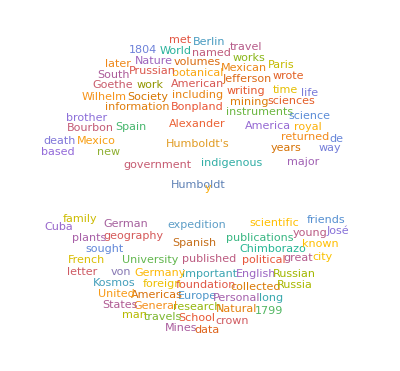

```mathematica
WordCloud[%]
```

Exercise: Calculate sin(π/3) to 10 digits of precision, 100 digits of precision, and infinite precision

## Structure of expressions

### 4-Rules of Wolfram Language

Capital letters on all command names.

Square brackets surround function arguments.

Curly braces are used for lists and ranges.

Shift+Enter to evaluate input

### FullForm and TreeForm [advanced]

General expressions in the Wolfram Language have an internal structure of the form Head[expr1, expr2, ...]. Some expressions seem not to follow this rule, however:

```mathematica
{1,2,3}
a+b
picture =-Graphics-
```

{1,2,3}

a+b

-Graphics-

Why do these expressions look different? The functions FullForm and TreeForm can help you understand what is happening.

```mathematica
FullForm[{1,2,3}]
```

List[1,2,3]

```mathematica
FullForm[a+b]
FullForm[a*b]
FullForm[a/b]
```

Plus[a,b]

Times[a,b]

Times[a,Power[b,-1]]

```mathematica
FullForm[-Graphics-]
```

Image[NumericArray[List[List[List[34,18,21,255],List[34,18,21,255],List[36,20,23,255],List[37,21,24,255],List[38,22,25,255],List[38,22,25,255],List[37,21,24,255],List[36,20,23,255],List[36,20,23,255],List[36,20,23,255],List[36,20,23,255],List[38,22,25,255],List[39,23,26,255],List[39,23,26,255],List[36,20,23,255],List[33,17,20,255],List[36,21,28,255],List[37,22,29,255],List[37,22,29,255],List[38,23,30,255],List[39,24,29,255],List[37,22,27,255],List[36,21,26,255],List[34,19,24,255],List[34,19,23,255],List[35,20,23,255],List[36,22,23,255],List[37,23,23,255],List[38,24,24,255],List[37,23,23,255],List[36,22,22,255],List[35,21,21,255],List[32,17,21,255],List[40,25,30,255],List[39,24,29,255],List[36,21,26,255],List[40,24,27,255],List[37,21,24,255],List[34,18,19,255],List[41,25,26,255],List[40,22,22,255],List[35,17,17,255],List[33,15,13,255],List[36,18,16,255],List[45,26,22,255],List[50,31,27,255],List[50,31,27,255],List[47,28,22,255],List[57,33,29,255],List[65,42,36,255],List[68,47,42,255],List[67,46,41,255],List[64,43,40,255],List[61,40,37,255],List[54,34,35,255],List[47,27,28,255],List[46,26,28,255],List[46,26,28,255],List[46,27,32,255],List[46,27,33,255],List[45,25,33,255],List[42,22,31,255],List[37,20,30,255],List[35,18,28,255],List[36,21,28,255],List[37,22,29,255],List[37,22,29,255],List[37,22,28,255],List[35,22,27,255],List[35,23,27,255],List[34,22,24,255],List[34,22,24,255],List[33,22,22,255],List[30,20,19,255],List[29,19,17,255],List[30,20,18,255],List[32,24,21,255],List[33,25,22,255],List[32,24,19,255],List[28,20,17,255],List[31,21,22,255],List[32,21,24,255],List[30,19,23,255],List[29,18,22,255],List[29,18,22,255],List[29,18,22,255],List[29,18,22,255],List[29,18,22,255],List[32,21,25,255],List[33,22,26,255],List[33,22,26,255],List[33,22,26,255],List[33,22,26,255],List[33,22,26,255],List[33,22,26,255],List[33,22,26,255],List[34,22,25,255],List[35,23,25,255],List[35,23,25,255],List[35,23,25,255],List[36,24,26,255],List[36,24,26,255],List[37,25,27,255],List[37,25,27,255],List[34,22,24,255],List[34,22,24,255],List[35,23,25,255]],148,List[List[14,15,19,255],List[14,15,19,255],List[15,16,20,255],List[15,16,20,255],List[13,14,18,255],List[11,12,16,255],96,List[17,18,22,255],List[8,9,13,255],List[14,15,19,255],List[15,16,20,255],List[15,16,20,255]]],""…""],3,Rule[1]]
 |  |  |  |

```mathematica
FullForm[(a+b^(-d)/√(c Sin[n π]))^z / Log[Tan[Exp[Cos[q]]]]]
```

Times[Power[Log[Tan[Power[E,Cos[q]]]],-1],Power[Plus[a,Times[Power[b,Times[-1,d]],Power[Times[c,Sin[Times[n,Pi]]],Rational[-1,2]]]],z]]

```mathematica
TreeForm[(a+b^(-d)/√(c Sin[n π]))^z / Log[Tan[Exp[Cos[q]]]]]
```

-Graphics-

```mathematica
TreeForm[{{1,2,3},{4,5,6}}]
```

-Graphics-

Exercise: Without using FullForm, write the full form of the following expression:
	Log[ ( -q + (x+y)^z ) / w]
    Check your answer with FullForm and TreeForm

## Lists

### What is a list?

In most cases, you are not working with one single output and one single output, and require some sort of structure for your data and calculations. In Wolfram Language, this construct is called the List and is represented with curly braces. 
Lists are very general objects that represent collection of expressions.
Lists can be used on their own, they can be inputs of functions, and they can be outputs of functions.

```mathematica
{1,2,3,4,5,6,7}
```

{1,2,3,4,5,6,7}

Lists can be nested:

```mathematica
{{1,2,3},{4,5,6},{7,8,9}}
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
MatrixForm[{{1,2,3},{4,5,6},{7,8,9}}]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

Lists need not be rectangular!

```mathematica
{1, {2,3}, {{4,5,6}, 7}};
MatrixForm[{1, {2,3}, {{4,5,6}, 7}}]
```

(1
{2,3}
{{4,5,6},7})

Any type of elements can be used in a list:

```mathematica
Alphabet["Greek"]
```

{α,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,μ,ν,ξ,ο,π,ρ,σ,τ,υ,φ,χ,ψ,ω}

A list can contain any combination of types of elements!

```mathematica
{1, 3.74,f[x],Plot[Sin[x],{x,0,2 Pi}], "Hello",picture }
```

{1,3.74,f[x],-Graphics-,Hello,-Graphics-}

### List index

Elements of the list can be indexed using double square brackets, which are shorthand for Part
The first element of a list corresponds to: 1

```mathematica
{1,7,9,4,5,8,2,3}[[3]]
Part[{1,7,9,4,5,8,2,3},3]
```

9

9

You can index lists starting from their ends by using negative indices:

```mathematica
{1,7,9,4,5,8,2,3}[[-1]]
```

3

Semicolons allow for extracting ranges from a list:

```mathematica
{1,7,9,4,5,8,2,3}[[3;;6]]
```

{9,4,5,8}

Lists can be indexed from point a to point b in steps of m by using the syntax: list[[a ;; b ;; m]]
	If you do not specify a, a value of 1 will be assumed.
	If you do not specify b, a value of -1 will be assumed.

```mathematica
{1,7,9,4,5,8,2,3}[[;;;;2]]
```

{1,9,5,2}

Braces allow for the extraction of specific, disparate elements:

```mathematica
{1,7,9,4,5,8,2,3}[[{2,3,7,-4}]]
```

{7,9,2,5}

For lists with more than one level, using only one index will work only at the top level:

```mathematica
{{1,2,3},{4,5,6},{7,8,9}}[[1]]
```

{1,2,3}

Using two indices allows you to access the second level of the list:

```mathematica
{{1,2,3},{4,5,6},{7,8,9}}[[3,1]]
```

7

### Operating on lists

```mathematica
{1,2,3}+5
```

{6,7,8}

```mathematica
{1,2,3}^3
```

{1,8,27}

```mathematica
{1,2,3}+{a,b,c}
```

{1+a,2+b,3+c}

```mathematica
Mean[{1,2,3}]
Total[{1,2,3}]
```

2

6

```mathematica
Sort[{3,1,2,5,4}]
```

{1,2,3,4,5}

```mathematica
Length[{1,2,3,4}]
Dimensions[{{1,2,3},{4,5,6}}]
MatrixForm[{{1,2,3},{4,5,6}}]
```

4

{2,3}

(1 | 2 | 3
4 | 5 | 6)

### Creating lists

```mathematica
RandomSample[{1,2,3,4,5}]
RandomSample[{1,2,3,4,5},3]
```

{3,2,1,5,4}

{4,1,5}

```mathematica
Range[19]
Range[6,14]
Range[0,7,0.5]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

{6,7,8,9,10,11,12,13,14}

{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.}

```mathematica
RandomInteger[{0,9},{2,3}]
RandomReal[{0,10},{3,2}]
```

{{5,5,2},{2,4,4}}

{{5.94054,6.28932},{8.38365,6.56653},{6.68065,0.0295989}}

Note: List can be arbitrarily deep:

```mathematica
MatrixForm[RandomInteger[{0,9},{5,4,3,2}]]
```

((6 | 5
6 | 1
7 | 9) | (5 | 1
5 | 7
3 | 1) | (6 | 6
4 | 1
4 | 9) | (5 | 0
8 | 1
6 | 7)
(8 | 2
8 | 7
4 | 7) | (0 | 9
4 | 2
9 | 3) | (0 | 8
6 | 5
5 | 2) | (1 | 0
9 | 1
2 | 5)
(5 | 3
4 | 0
6 | 1) | (7 | 3
8 | 4
2 | 0) | (0 | 7
9 | 7
3 | 3) | (1 | 0
7 | 2
6 | 2)
(5 | 3
0 | 9
5 | 7) | (5 | 4
0 | 0
3 | 1) | (5 | 5
5 | 5
0 | 3) | (1 | 8
9 | 3
0 | 3)
(7 | 0
1 | 3
4 | 8) | (1 | 1
7 | 9
3 | 9) | (6 | 6
1 | 3
8 | 5) | (6 | 9
7 | 7
5 | 0))

You can reshape lists with ArrayReshape

```mathematica
ArrayReshape[{{1,2,3,4},{5,6,7,8},{9,10,11,12}},{2,6}]
```

{{1,2,3,4,5,6},{7,8,9,10,11,12}}

Exercise: 
Create a list of random integer that is at least three levels deep and has at least three elements at each level. 
After creating this list, display its matrix form.
Then, extract the second element of each of the first and last element of the third element of the main list.
Hint: Read the indices from the end if these instructions seem confusing.

## Tips and Tricks

Many expressions are automatically color-coded:

Blue symbols are undefined.

Black symbols are defined (either by you or the system).

Teal symbols, inside of named or pure functions, represent variables.

Lavender brackets have not been closed.

The various braces are confusing - here is a quick guide:

(Parentheses) are used only for grouping, e.g. (a+b)^c

{Curly braces} are used for lists, e.g. {1,2,3}

[Single square brackets] are used for functions, e.g. f[x]

[[Double square brackets]] are used for indexing, e.g. list[[3]]

You do not always want to see an output for every input. Imagine for instance defining a 10,000x10,000 matrix, it would be best not to print that out into the notebook environment. Use a semicolon (;) at the end of a line to suppress its output.

Use Clear to clear value and definitions

The ? operator ( =  Information ) operator can be used to ask the WL to display any information it knows about a symbol.

When in doubt, consult the documentation!

## Useful links

Fast Introduction for Programmers

Wolfram Language Syntax

Notebook Formatting and Styling

Constructing Lists